```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be zero. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity[a_,filename_,flag_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros},

(*count the number of zeros depending upon the format of the matrix*)
numzeros = If[Count[a,0,Infinity]==0,Count[a,0.0,Infinity],Count[a,0,Infinity]];
nnz = Length[Flatten[a]]-numzeros;

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;nnz]];

rowindicies = ConstantArray[0,nnz];
colindicies = ConstantArray[0,nnz];
entries = ConstantArray[0,nnz];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]]-1,{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]]-1,{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["../system_matrices/",filename]];

WriteString[str,ToString[nnz],"\n"];

Which[flag == 0,
Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[0],"\n"],{ii,1,Length[rowindicies]}];,
flag == 1,
Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];
]

Close[str];

]
```

## Project individual tensors

The following function develos the projector for tensors of a particular degree

```mathematica
ProjectTensor[degree_,nx_,ny_]:=Module[{result},
Which[degree == 0,
result = 1,
degree == 1,
result = {nx,ny,-ny,nx};
result=ArrayReshape[result,{2,2}];,
degree == 2,
result = {nx*nx,2*nx*ny,ny*ny,-nx*ny,nx*nx-ny*ny,nx*ny,ny*ny,-2*nx*ny,nx*nx};
result=ArrayReshape[result,{3,3}];,
degree == 3,
result = {nx*nx*nx,3*ny*nx*nx,3*nx*ny*ny,ny*ny*ny,-ny*nx*nx,nx*nx*nx-2*nx*ny*ny,2*ny*nx*nx-ny*ny*ny,nx*ny*ny,nx*ny*ny,-2*ny*nx*nx+ny*ny*ny,nx*nx*nx-2*nx*ny*ny,ny*nx*nx,-ny*ny*ny,3*nx*ny*ny,-3*ny*nx*nx,nx*nx*nx};
result=ArrayReshape[result,{4,4}];
];


result
]
```

## Boundary Matrices

```mathematica
BoundaryMatrices[Ax_,B_,nEqn_,nBC_]:=Module[{RAx,λAx,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,RAxsorted,RAxplus,RAxminus,BtildeInv,Bhat},

{λAx,RAx} =Chop[Eigensystem[Ax]];
RAx = Transpose[RAx];

Positionλneg = Flatten[Position[λAx,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λAx,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λAx,_?(#==0&)]];
numλzero = Length[Positionλzero];


(*sorting the eigen vectors*)
RAxsorted=ConstantArray[0,{nEqn,nEqn}];
RAxsorted[[All,1;;numλneg]]=RAx[[All,Positionλneg]];
RAxsorted[[All,numλneg+1;;numλneg+numλzero]]=RAx[[All,Positionλzero]];
RAxsorted[[All,numλneg+numλzero+1;;nEqn]]=RAx[[All,Positionλpos]];
RAx = RAxsorted;

λAx = Chop[Diagonal[Inverse[RAx].Ax.RAx]];

RAxplus = RAx[[All,numλneg+numλzero+1;;nEqn]];
RAxminus = RAx[[All,1;;numλneg]];

BtildeInv = ConstantArray[0,{nBC,nBC}];
BtildeInv = Inverse[B.RAxminus];

Bhat = ConstantArray[0,{nEqn,nEqn}];
Bhat = RAxminus.BtildeInv.B;

{RAx,λAx,BtildeInv,Bhat}
]
```

## Boundary Matrices (Dummy)

```mathematica
BoundaryMatricesDummy[Ax_,B_,nEqn_,nBC_]:=Module[{RAx,λAx,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,RAxsorted,RAxplus,RAxminus,BtildeInv,Bhat,R},

{λAx,RAx} =Chop[Eigensystem[Ax]];
RAx = Transpose[RAx];

Positionλneg = Flatten[Position[λAx,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λAx,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λAx,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
RAxsorted=ConstantArray[0,{nEqn,nEqn}];
RAxsorted[[All,1;;numλneg]]=RAx[[All,Positionλneg]];
RAxsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
RAxsorted[[All,numλneg+numλzero+1;;nEqn]]=RAx[[All,Positionλpos]];
RAx = RAxsorted;

λAx = Chop[Diagonal[Inverse[RAx].Ax.RAx]];

RAxplus = RAx[[All,numλneg+numλzero+1;;nEqn]];
RAxminus = RAx[[All,1;;numλneg]];

BtildeInv = ConstantArray[0,{nBC,nBC}];
R = ConstantArray[0,{nBC,nBC}];
BtildeInv = Inverse[B.RAxminus];

Bhat = ConstantArray[0,{nEqn,nEqn}];
Bhat = RAxminus.BtildeInv.B;

R = BtildeInv .B.RAxplus;
{RAx,λAx,BtildeInv,Bhat,R}
]
```

# System A

```mathematica
neqnA = 6;
```

## entropy

```mathematica
entropyA = Simplify[1/2(θ^2+qx^2+qy^2+Rxx^2+Ryy^2+2 Rxy^2+(Rxx+Ryy)^2)];
UA = {θ,qx,qy,Rxx,Rxy,Ryy};
symmetrizerA = D[D[entropyA,{UA}],{UA}];
Eigenvalues[symmetrizerA]
symmetrizerA//MatrixForm
symmetrizerA.Ax//MatrixForm
developsparsity[N[symmetrizerA],"6S.txt",1];
```

{3,2,1,1,1,1}

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 2)

(0. | 1. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

## Projector Matrix

```mathematica
Projector[nx_,ny_]:=Module[{result},

result = ConstantArray[0,{6,6}];

result[[1,1]]=1.0;
result[[2,2]]=nx;
result[[2,3]]=ny;
result[[3,2]]=-ny;
result[[3,3]]=nx;
result[[4,4]]=nx*nx;
result[[4,5]]=2*nx*ny;
result[[4,6]]=ny*ny;
result[[5,4]]=-nx*ny;
result[[5,5]]=nx*nx-ny*ny;
result[[5,6]]=nx*ny;
result[[6,4]]=ny*ny;
result[[6,5]]=-2*nx*ny;
result[[6,6]]=nx*nx;

result

]
```

## BC matrix

```mathematica
BCrhs = Flatten[ConstantArray[0,{6,1}]];

BoundaryMatrix[chi_]:=Module[{BC},
BC = ConstantArray[0,{6,6}];
BC[[1,1]]=1.0;
BC[[2,1]]=chi;
BC[[2,4]]=1.0*chi;
BC[[3,3]]=1.0;
BC[[4,4]]=1.0;
BC[[5,3]]=chi;
BC[[6,6]]=1.0;

BC
]



BCrhs[[2]]=chi*theta0;
BCrhs[[5]]=uW*p[1];
```

```mathematica
BCrhs//MatrixForm
BoundaryMatrix[1]//MatrixForm
```

(0
chi theta0
0
0
uW p[1]
0)

(1. | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1. | 0 | 0
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.)

## B matrix

```mathematica
B = ConstantArray[0,{2,neqnA}];
B = {{-1,1,0,-1,0,0},{0,0,-1,0,1,0}};
developsparsity[N[B,10],"6B.txt",1]
```

## Ax and Ay

```mathematica
Ax = ConstantArray[0,{6,6}];
Ay = ConstantArray[0,{6,6}];
```

```mathematica
Ax[[1,2]]=1.0;
Ax[[2,1]]=1.0;
Ax[[2,4]]=1.0;
Ax[[3,5]]=1.0;
Ax[[4,2]]=2/3;
Ax[[5,3]]=1/2;
Ax[[6,2]]=-1/3;

Ay[[1,3]]=1.0;
Ay[[2,5]] = 1.0;
Ay[[3,1]] =1.0;
Ay[[3,6]] = 1.0;
Ay[[4,3]] =-1/3 ;
Ay[[5,2]]=1/2;
Ay[[6,3]] = 2/3;

(*developsparsity[N[Ax,15],"6A1.txt",1]
developsparsity[N[Ay,15],"6A2.txt",1]*)
```

```mathematica
Ax//MatrixForm
Ay//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0
1. | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 0 | 0)

(0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
1. | 0 | 0 | 0 | 0 | 1.
0 | 0 | -1/3 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 2/3 | 0 | 0 | 0)

## Production term

```mathematica
valuesdiagonal = {0,1,1,1,1,1};

P =DiagonalMatrix[valuesdiagonal];

developsparsity[N[P],"6P.txt",1];
P//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

## An

```mathematica
An = Ax nx + Ay ny;
developsparsity[An,"6An.txt",0];
An//MatrixForm
```

(0. | 0.+1. nx | 1. ny | 0. | 0. | 0.
0.+1. nx | 0. | 0. | 0.+1. nx | 1. ny | 0.
1. ny | 0. | 0. | 0. | 0.+1. nx | 1. ny
0. | 0.+(2 nx)/3 | -0.333333 ny | 0. | 0. | 0.
0. | 0.5 ny | 0.+nx/2 | 0. | 0. | 0.
0. | 0.-nx/3 | 0.666667 ny | 0. | 0. | 0.)

## |S.An|

```mathematica
SAn =TrigReduce[ Simplify[symmetrizerA.Projector[nx,-ny].Ax.Projector[nx,ny]]/.{nx->Cos[θ],ny->Sin[θ]}];
N[Eigenvalues[SAn]]
```

{0.,0.,Root[8.66667+2. Cos[4 θ]-4. #1^2+0.333333 #1^4&,1],Root[8.66667+2. Cos[4 θ]-4. #1^2+0.333333 #1^4&,2],Root[8.66667+2. Cos[4 θ]-4. #1^2+0.333333 #1^4&,3],Root[8.66667+2. Cos[4 θ]-4. #1^2+0.333333 #1^4&,4]}

## Sqrt(S)

```mathematica
SqrtsymmetrizerA = MatrixPower[symmetrizerA,1/2];
SqrtsymmetrizerA//MatrixForm
developsparsity[N[SqrtsymmetrizerA,15],"6S_half.txt",1]
```

(√2 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | √(3/2)+1/(√2) | 0 | √(3/2)-1/(√2)
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | √(3/2)-1/(√2) | 0 | √(3/2)+1/(√2))

## Inv(Sqrt(S))

```mathematica
InvSqrtsymmetrizerA = MatrixPower[symmetrizerA,-1/2];
InvSqrtsymmetrizerA//MatrixForm
developsparsity[N[InvSqrtsymmetrizerA,15],"6S_half_inv.txt",1];
```

(1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2)+1/(2 √6) | 0 | -1/(2 √2)+1/(2 √6)
0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/(2 √2)+1/(2 √6) | 0 | 1/(2 √2)+1/(2 √6))

## Proj.Inv(Sqrt(S))

```mathematica
CForm[Flatten[Simplify[Projector[nx,ny].MatrixPower[symmetrizerA,-0.5]]]]
```

List(1.,0.,0.,0.,0.,0.,0.,0. + 1.*nx,0. + 1.*ny,0.,0.,0.,0.,0. - 1.*ny,0. + 1.*nx,0.,0.,0.,0.,0.,0.,
   0. + 0.7886751345948129*Power(nx,2) - 0.21132486540518713*Power(ny,2),0. + 1.4142135623730951*nx*ny,
   0. - 0.21132486540518713*Power(nx,2) + 0.7886751345948129*Power(ny,2),0.,0.,0.,0. - 1.*nx*ny,
   0. + 0.7071067811865476*Power(nx,2) - 0.7071067811865476*Power(ny,2),0. + 1.*nx*ny,0.,0.,0.,
   0. - 0.21132486540518713*Power(nx,2) + 0.7886751345948129*Power(ny,2),0. - 1.4142135623730951*nx*ny,
   0. + 0.7886751345948129*Power(nx,2) - 0.21132486540518713*Power(ny,2))

## Inv(Proj.Inv(Sqrt(S)))

```mathematica
CForm[Flatten[Simplify[MatrixPower[symmetrizerA,0.5].Projector[nx,-ny]]]]
```

List(1.,0.,0.,0.,0.,0.,0.,0. + 1.*nx,0. - 1.*ny,0.,0.,0.,0.,0. + 1.*ny,0. + 1.*nx,0.,0.,0.,0.,0.,0.,
   0. + 1.3660254037844386*Power(nx,2) + 0.3660254037844386*Power(ny,2),0. - 2.*nx*ny,
   0. + 0.3660254037844386*Power(nx,2) + 1.3660254037844386*Power(ny,2),0.,0.,0.,0. + 1.4142135623730951*nx*ny,
   0. + 1.4142135623730951*Power(nx,2) - 1.4142135623730951*Power(ny,2),0. - 1.4142135623730951*nx*ny,0.,0.,0.,
   0. + 0.3660254037844386*Power(nx,2) + 1.3660254037844386*Power(ny,2),0. + 2.*nx*ny,
   0. + 1.3660254037844386*Power(nx,2) + 0.3660254037844386*Power(ny,2))

## Aminus1D

```mathematica
Aminus1D = Transpose[Eigenvectors[Ax]].(DiagonalMatrix[Abs[Eigenvalues[Ax]]]-DiagonalMatrix[Eigenvalues[Ax]]).Inverse[Transpose[Eigenvectors[Ax]]];
```

## Aminus

```mathematica
CForm[Flatten[Chop[Simplify[MatrixPower[symmetrizerA,0.5].Projector[nx,-ny].Aminus1D.Projector[nx,ny].MatrixPower[symmetrizerA,-0.5]]]]]
```

List(0.7745966692414835,-0.9999999999999998*nx,-0.9999999999999998*ny,
   0.6109051323707205*Power(nx,2) - 0.16369153687076268*Power(ny,2),1.095445115010332*nx*ny,
   -0.16369153687076268*Power(nx,2) + 0.6109051323707205*Power(ny,2),-1.0000000000000002*nx,
   1.2909944487358054*Power(nx,2) + 0.7071067811865482*Power(ny,2),0.5838876675492571*nx*ny,
   -0.7886751345948126*Power(nx,3) - 0.7886751345948138*nx*Power(ny,2),
   -0.7071067811865467*Power(nx,2)*ny - 0.7071067811865482*Power(ny,3),
   0.21132486540518708*Power(nx,3) + 0.21132486540518822*nx*Power(ny,2),-1.0000000000000002*ny,
   0.5838876675492571*nx*ny,0.7071067811865482*Power(nx,2) + 1.2909944487358054*Power(ny,2),
   0.21132486540518822*Power(nx,2)*ny + 0.21132486540518708*Power(ny,3),
   -0.7071067811865482*Power(nx,3) - 0.7071067811865467*nx*Power(ny,2),
   -0.7886751345948138*Power(nx,2)*ny - 0.7886751345948126*Power(ny,3),
   0.6109051323707209*Power(nx,2) - 0.1636915368707628*Power(ny,2),
   -0.7886751345948129*Power(nx,3) - 0.7886751345948132*nx*Power(ny,2),
   0.21132486540518736*Power(nx,2)*ny + 0.21132486540518705*Power(ny,3),
   0.4818056874971401*Power(nx,4) + 1.1560146726259342*Power(nx,2)*Power(ny,2) + 
    0.034592091997182155*Power(ny,4),-0.1360496764779962*Power(nx,3)*ny + 0.768505208511672*nx*Power(ny,3),
   -0.12909944487358058*Power(nx,4) - 0.8978157828787732*Power(nx,2)*Power(ny,2) - 
    0.12909944487358055*Power(ny,4),1.0954451150103326*nx*ny,
   -0.7071067811865472*Power(nx,2)*ny - 0.7071067811865477*Power(ny,3),
   -0.7071067811865477*Power(nx,3) - 0.7071067811865472*nx*Power(ny,2),
   -0.13604967647799626*Power(nx,3)*ny + 0.768505208511672*nx*Power(ny,3),
   0.7071067811865477*Power(nx,4) + 0.1349797761098713*Power(nx,2)*Power(ny,2) + 0.7071067811865477*Power(ny,4),
   0.768505208511672*Power(nx,3)*ny - 0.13604967647799626*nx*Power(ny,3),
   -0.1636915368707628*Power(nx,2) + 0.6109051323707209*Power(ny,2),
   0.21132486540518705*Power(nx,3) + 0.21132486540518736*nx*Power(ny,2),
   -0.7886751345948132*Power(nx,2)*ny - 0.7886751345948129*Power(ny,3),
   -0.12909944487358055*Power(nx,4) - 0.8978157828787732*Power(nx,2)*Power(ny,2) - 
    0.12909944487358058*Power(ny,4),0.768505208511672*Power(nx,3)*ny - 0.1360496764779962*nx*Power(ny,3),
   0.034592091997182155*Power(nx,4) + 1.1560146726259342*Power(nx,2)*Power(ny,2) + 
    0.4818056874971401*Power(ny,4))

# System B

```mathematica
nEqnB = 10;
nBC = 4;
```

## Projector Matrix

```mathematica
Projector = ConstantArray[0,{nEqnB,nEqnB}];


Projector[[1,1]]=1.0;
Projector[[2,2]]=nx;
Projector[[2,3]]=ny;
Projector[[3,2]]=-ny;
Projector[[3,3]]=nx;
Projector[[4,4]]=nx nx;
Projector[[4,5]]=2*nx*ny;
Projector[[4,6]]=ny ny;
Projector[[5,4]]=-nx*ny;
Projector[[5,5]]=nx nx-ny ny;
Projector[[5,6]]=nx*ny;
Projector[[6,4]]=ny ny;
Projector[[6,5]]=-2*nx*ny;
Projector[[6,6]]=nx nx;
Projector[[7,7]]=nx*nx nx;
Projector[[7,8]]=3*ny*nx nx;
Projector[[7,9]]=3*nx*ny ny;
Projector[[7,10]]=ny*ny ny;
Projector[[8,7]]=-ny*nx nx;
Projector[[8,8]]=nx*nx nx-2*nx*ny ny;
Projector[[8,9]]=2*ny*nx nx-ny*ny ny;
Projector[[8,10]]=nx*ny ny;
Projector[[9,7]]=nx*ny ny;
Projector[[9,8]]=-2*ny*nx nx+ny*ny ny;
Projector[[9,9]]=nx*nx nx-2*nx*ny ny;
Projector[[9,10]]=ny*nx nx;
Projector[[10,7]]=-ny*ny ny;
Projector[[10,8]]=3*nx*ny ny;
Projector[[10,9]]=-3*ny*nx nx;
Projector[[10,10]]=nx*nx nx;
```

## System Matrix

```mathematica
Ax = ConstantArray[0,{nEqnB,nEqnB}];

Ax[[1,2]]=1.0;
Ax[[2,1]]=1.0;
Ax[[2,4]]=1.0;
Ax[[3,5]]=1.0;
Ax[[4,2]]=4.0/3;
Ax[[4,7]]=2.0;
Ax[[5,8]]=2.0;
Ax[[5,3]]=1.0;
Ax[[6,2]]=-2.0/3;
Ax[[6,9]]=2.0;
Ax[[7,4]]=3.0/5;
Ax[[8,5]]=8.0/15;
Ax[[9,6]]=1.0/3;
Ax[[9,4]]=-2.0/15;
Ax[[10,5]]=-2.0/5;


Ay = Inverse[(Projector/.{nx->0,ny->1})].Ax.(Projector/.{nx->0,ny->1});
Ax//MatrixForm//TraditionalForm
Ay//MatrixForm//TraditionalForm

ArrayRules[Ax]//MatrixForm//TraditionalForm
ArrayRules[Ay]//MatrixForm//TraditionalForm

developsparsity[N[Ax,10],"10A1.txt",1]
developsparsity[N[Ay,10],"10A2.txt",1]
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 1.33333 | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 2. | 0 | 0
0 | -0.666667 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 0
0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.533333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.133333 | 0 | 0.333333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0)

Projector.(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 1.33333 | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 2. | 0 | 0
0 | -0.666667 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 0
0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.533333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.133333 | 0 | 0.333333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0).Projector

({1,2}→1.
{2,1}→1.
{2,4}→1.
{3,5}→1.
{4,2}→1.33333
{4,7}→2.
{5,3}→1.
{5,8}→2.
{6,2}→-0.666667
{6,9}→2.
{7,4}→0.6
{8,5}→0.533333
{9,4}→-0.133333
{9,6}→0.333333
{10,5}→-0.4
{_,_}→0)

ArrayRules::rect: Nonrectangular array encountered.

ArrayRules[Projector.(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 1.33333 | 0 | 0 | 0 | 0 | 2. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 2. | 0 | 0
0 | -0.666667 | 0 | 0 | 0 | 0 | 0 | 0 | 2. | 0
0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.533333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.133333 | 0 | 0.333333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.4 | 0 | 0 | 0 | 0 | 0).Projector]

developsparsity[{{0,1.,0,0,0,0,0,0,0,0},{1.,0,0,1.,0,0,0,0,0,0},{0,0,0,0,1.,0,0,0,0,0},{0,1.33333,0,0,0,0,2.,0,0,0},{0,0,1.,0,0,0,0,2.,0,0},{0,-0.666667,0,0,0,0,0,0,2.,0},{0,0,0,0.6,0,0,0,0,0,0},{0,0,0,0,0.533333,0,0,0,0,0},{0,0,0,-0.133333,0,0.333333,0,0,0,0},{0,0,0,0,-0.4,0,0,0,0,0}},10A1.txt,1]

developsparsity[Inverse[Projector].{{0,1.,0,0,0,0,0,0,0,0},{1.,0,0,1.,0,0,0,0,0,0},{0,0,0,0,1.,0,0,0,0,0},{0,1.33333,0,0,0,0,2.,0,0,0},{0,0,1.,0,0,0,0,2.,0,0},{0,-0.666667,0,0,0,0,0,0,2.,0},{0,0,0,0.6,0,0,0,0,0,0},{0,0,0,0,0.533333,0,0,0,0,0},{0,0,0,-0.133333,0,0.333333,0,0,0,0},{0,0,0,0,-0.4,0,0,0,0,0}}.Projector,10A2.txt,1]

## Production term

```mathematica
valuesdiagonal = {0,1,1,1,1,1,1,1,1,1,1};
P = DiagonalMatrix[valuesdiagonal];
developsparsity[N[P],"10P.txt",1];
```

## Boundary condition matrix

```mathematica
X0 = ConstantArray[0,{nEqnB,nBC}];
X0[[2,1]] = 1;
X0[[5,2]] = 1;
X0[[7,3]]=1;
X0[[9,4]]=1;

(*BC is BC.U = g*)
BC = ConstantArray[0,{nBC,nEqnB}];

BC[[1,1]]=chi;
BC[[1,2]]=-1.0;
BC[[2,3]]=chi;
BC[[2,5]]=-1.0;
BC[[2,8]]=kappa*chiW;
BC[[3,4]]=chi;
BC[[3,7]]=-1.0;
BC[[4,6]]=chi;
BC[[4,9]]=-1.0;

U = {θ,qn,qt,Rnn,Rnt,Rtt,ψnnn,ψnnt,ψntt,ψttt};


(*Developing BC to the BC in u = BC.u - g*)
BCnew = CoefficientArrays[{θ==0,χ θ==0,qt==0,Rnn==0,χ qt+2 * χ * ψnnt== 0,Rtt==0,χ Rnn==0,ψnnt==0,χ Rtt == 0,ψttt==0},U][[2]];

(*Converting BCnew to a full matrix*)
BCnew2 = ConstantArray[0,{10,10}];

Do[Do[If[(BCnew[[ii,jj]]/.χ->1)≠0,BCnew2[[ii,jj]]=BCnew[[ii,jj]]],{jj,1,nEqnB}],{ii,1,nEqnB}];

BC.U//MatrixForm
BCnew//MatrixForm
(U-BCnew.U)//MatrixForm
ArrayRules[BCnew]
developsparsity[N[BCnew2/.{χ->1}],"10BC.txt",1]
```

(-1. qn+chi θ
chi qt-1. Rnt+chiW kappa ψnnt
chi Rnn-1. ψnnn
chi Rtt-1. ψntt)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | χ | 0 | 0 | 0 | 0 | 2 χ | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0
qn-θ χ
0
0
Rnt-qt χ-2 χ ψnnt
0
-Rnn χ+ψnnn
0
-Rtt χ+ψntt
0)

{{1,1}→1,{2,1}→χ,{3,3}→1,{4,4}→1,{5,3}→χ,{5,8}→2 χ,{6,6}→1,{7,4}→χ,{8,8}→1,{9,6}→χ,{10,10}→1,{_,_}→0}

developsparsity[{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,2.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},10BC.txt,1]

# A^-.BC(only implemented for A system)

```mathematica
plottingeigenvalues[nx_,ny_,typeBC_,typeFlux_]:=Module[{nEqn,An,RAn,λAn,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,RAnsorted,RAnplus,RAnminus,diffusion,D,Aminus,B,BCcharacteristic,AminusBC},

nEqn = 6;
An = symmetrizerA.(Ax nx+Ay ny);
{λAn,RAn} = Chop[Eigensystem[An]];
RAn = Transpose[RAn];

Positionλneg = Flatten[Position[λAn,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λAn,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λAn,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigenvalues*)
λAn=Sort[λAn];

(*sorting the eigen vectors*)
RAnsorted=ConstantArray[0,{nEqn,nEqn}];
RAnsorted[[All,1;;numλneg]]=RAn[[All,Positionλneg]];
RAnsorted[[All,numλneg+1;;numλneg+numλzero]]=RAn[[All,Positionλzero]];
RAnsorted[[All,numλneg+numλzero+1;;nEqn]]=RAn[[All,Positionλpos]];
RAn = RAnsorted;

RAnplus = RAn[[All,numλneg+numλzero+1;;nEqn]];
RAnminus = RAn[[All,1;;numλneg]];

Which[typeFlux==0,
diffusion =Flatten[Max[Abs[λAn]]ConstantArray[1,{1,nEqn}]];,
typeFlux==1,
diffusion =Abs[λAn];
];

D = RAn.DiagonalMatrix[diffusion].Inverse[RAn];
Aminus = Chop[An-D];

(*the matrix of the boundary conditions B.U=g*)
B={{-1,1,0,-1,0,0},{0,0,-1,0,1,0}};

(*BC obtained by characteristic decomposition*)
BCcharacteristic = IdentityMatrix[nEqn];
Do[BCcharacteristic[[ii,ii]]=0,{ii,1,Length[numλneg]}];
BCcharacteristic[[{1,Length[Positionλneg]},{-Length[Positionλpos],-1}]] = DiagonalMatrix[λAn[[1;;numλneg]]-Abs[λAn[[1;;numλneg]]]].Inverse[B.RAnminus].B.RAnplus;

BCcharacteristic = RAn.BCcharacteristic.Transpose[RAn].Projector[nx,-ny];

Which[typeBC == 0,
AminusBC =Aminus.BCcharacteristic;,
typeBC == 1,
AminusBC=Aminus.BoundaryMatrix[1];];

{Det[B.RAnminus],Eigenvalues[D+AminusBC+Transpose[D+AminusBC]]}
]
```

```mathematica
θ = Range[0,2π,0.01];
```

### Determinant[B.RAnminus]

{}

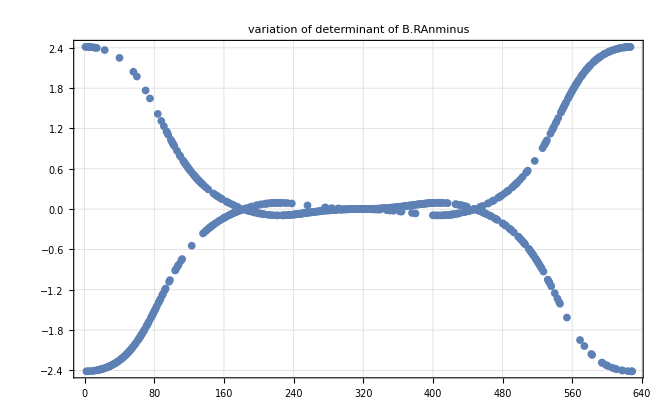

```mathematica
determinantBRAnminus = Table[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],1,1][[1]],{ii,1,Length[θ]}];
Position[determinantBRAnminus,_?(#==0&)]
ListPlot[determinantBRAnminus,PlotRange->Full,GridLines->Automatic,Frame->True,PlotLabel->"variation of determinant of B.RAnminus"]
```

### BC with Upwind

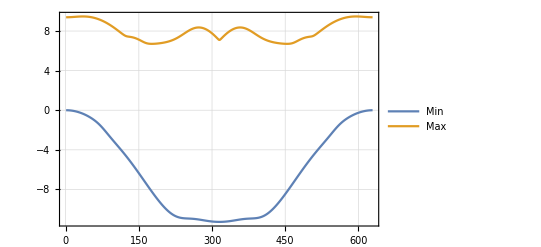

```mathematica
MineigenvaluesAminusBC = Table[Min[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],1,1][[2]]],{ii,1,Length[θ]}];
MaxeigenvaluesAminusBC = Table[Max[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],1,1][[2]]],{ii,1,Length[θ]}];
ListPlot[{MineigenvaluesAminusBC,MaxeigenvaluesAminusBC},PlotRange->Full,Joined->True,Frame->True,GridLines->Automatic,PlotLegends->{"Min","Max"}]
```

### BC with LLF

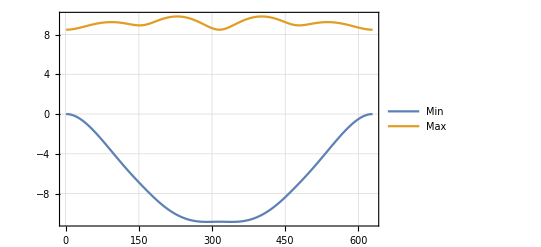

```mathematica
MineigenvaluesAminusBC = Table[Min[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],1,0][[2]]],{ii,1,Length[θ]}];
MaxeigenvaluesAminusBC = Table[Max[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],1,0][[2]]],{ii,1,Length[θ]}];
ListPlot[{MineigenvaluesAminusBC,MaxeigenvaluesAminusBC},PlotRange->Full,Joined->True,Frame->True,GridLines->Automatic,PlotLegends->{"Min","Max"}]
```

### BCcharacteristic with Upwind

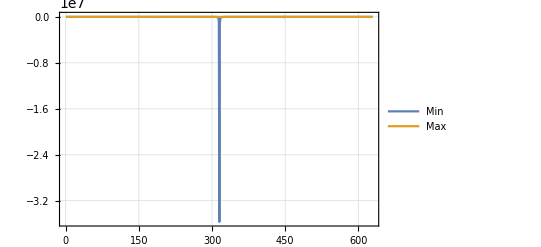

```mathematica
MineigenvaluesAminusBC = Table[Min[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],0,1][[2]]],{ii,1,Length[θ]}];
MaxeigenvaluesAminusBC = Table[Max[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],0,1][[2]]],{ii,1,Length[θ]}];
ListPlot[{MineigenvaluesAminusBC,MaxeigenvaluesAminusBC},PlotRange->Full,Joined->True,Frame->True,GridLines->Automatic,PlotLegends->{"Min","Max"}]
```

### BCcharacteristic with LLF

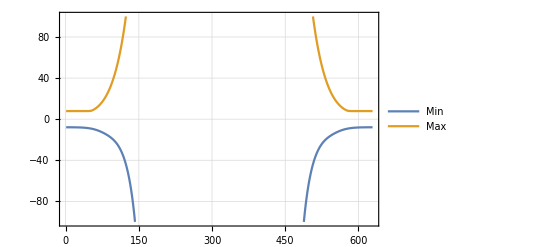

```mathematica
MineigenvaluesAminusBC = Table[Min[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],0,0]],{ii,1,Length[θ]}];
MaxeigenvaluesAminusBC = Table[Max[plottingeigenvalues[Cos[θ[[ii]]],Sin[θ[[ii]]],0,0]],{ii,1,Length[θ]}];
ListPlot[{MineigenvaluesAminusBC,MaxeigenvaluesAminusBC},PlotRange->{Full,{-100,100}},Joined->True,Frame->True,GridLines->Automatic,PlotLegends->{"Min","Max"}]
```

# R13

```mathematica
neqnR13 = 17;
nbc13 = 6;
(*variables that are used to derive the system. Ref. Manuel's paper*)
WR13 =  {w0,wn,wt,w1,wnn,wnt,wtt,w1n,w1t,wnnn,wnnt,wntt,wttt,w2,w1nn,w1nt,w1tt};

(*CAUTION: These variables are not the variable directly used in the equations, see the git hub repository for the exact definition of the variables*)
UR13 = {ρ,vn,vt,θ,σnn,σnt,σtt,qn,qt,mnnn,mnnt,mntt,mttt,Δ,Rnn,Rnt,Rtt};
```

## Projector

```mathematica
Projector13[nx_,ny_]:=Module[{result,tensor0,tensor1,tensor2,tensor3},

(*First we will create the projectors for tensors of a particular degree*)
tensor0 = ProjectTensor[0,nx,ny];
tensor1 = ProjectTensor[1,nx,ny];
tensor2 = ProjectTensor[2,nx,ny];
tensor3 = ProjectTensor[3,nx,ny];

result = ConstantArray[0,{neqnR13,neqnR13}];
result[[1,1]]=tensor0;
     result[[2;;3,2;;3]]=tensor1;
result[[4,4]]=tensor0;
result[[5;;7,5;;7]]=tensor2;
result[[8;;9,8;;9]]=tensor1;
result[[10;;13,10;;13]]=tensor3;
result[[14,14]] = tensor0;
result[[15;;17,15;;17]] = tensor2;

result
]

Projector13[nx,ny]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | nx | ny | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ny | nx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | nx^2 | 2 nx ny | ny^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -nx ny | nx^2-ny^2 | nx ny | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ny^2 | -2 nx ny | nx^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | nx | ny | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ny | nx | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | nx^3 | 3 nx^2 ny | 3 nx ny^2 | ny^3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -nx^2 ny | nx^3-2 nx ny^2 | 2 nx^2 ny-ny^3 | nx ny^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | nx ny^2 | -2 nx^2 ny+ny^3 | nx^3-2 nx ny^2 | nx^2 ny | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ny^3 | 3 nx ny^2 | -3 nx^2 ny | nx^3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | nx^2 | 2 nx ny | ny^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -nx ny | nx^2-ny^2 | nx ny
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ny^2 | -2 nx ny | nx^2)

## Ax and Ay

```mathematica
AxR13 = ConstantArray[0,{neqnR13,neqnR13}];

AxRow13 ={1,0,3,1,4,1,5,2,6,7,7,6,4,3,8,5,9,4,10,5,11,11,6,12,13,7,14,7,15,8,16};
AxCol13 = {0,1,1,3,1,4,2,5,1,3,4,7,7,7,5,8,4,9,5,10,6,4,11,5,7,13,7,14,8,15,7};
AxVal13 = {1,1,-1,-0.6666666666666666,1.3333333333333333,1,1,1,-0.6666666666666666,1.6666666666666667,-1,0.26666666666666666,-0.5333333333333333,1,-1,-0.4,1.8,1,1.6,1,1,-0.4,1,-1.2,-2,-0.6666666666666666,1.8666666666666667,1,1.4,1,-0.9333333333333333};

Do[AxR13[[AxRow13[[ii]]+1,AxCol13[[ii]]+1]]=AxVal13[[ii]],{ii,1,Length[AxRow13]}];

AyR13 = Projector13[0,-1].AxR13.Projector13[0,1];


developsparsity[N[AxR13,15],"17A1.txt",1]
developsparsity[N[AyR13,15],"17A2.txt",1]
```

## Production(not divided by tau)

```mathematica
P13 = ConstantArray[0,{neqnR13,neqnR13}];
diagonal13 = {0,0,0,0,1,1,1,0.6666666666666666,0.6666666666666666,1.5,1.5,1.5,1.5,0.6666666666666666,1.1666666666666667,1.1666666666666667,1.1666666666666667};
P13 = DiagonalMatrix[diagonal13];

developsparsity[N[P13,15],"17P.txt",1]
```

## B (Boundary Matrix)

```mathematica
BR13 = ConstantArray[0,{nbc13,neqnR13}];
BRow13 = {0,0,1,3,2,0,4,4,3,2,0,5,1,4,2,5,1,3,5,1,4,4,3,2,4,3,2,5};
BCol13 = {0,1,2,3,3,3,4,3,4,4,4,2,5,6,7,8,8,9,10,10,11,13,13,13,14,14,14,15};
BVal13 = {-1,1,-1,-0.26666666666666666,-1.3333333333333333,0.6666666666666666,0.2,0.13333333333333333,-1.4,0.5,-1,-0.5,1,-1,1,-1.1,0.2,1,-0.5,-1,1,-0.05333333333333334,0.10666666666666667,0.5333333333333333,0.08,-0.16,-0.8,1};

Do[BR13[[BRow13[[ii]]+1,BCol13[[ii]]+1]] = BVal13[[ii]],{ii,1,Length[BRow13]}];

developsparsity[N[BR13,15],"17B.txt",1]
BR13.WR13//MatrixForm
```

developsparsity[{{-1.,1.,0,0.666667,-1.,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1.,0,0,1.,0,0,0.2,0,-1.,0,0,0,0,0,0},{0,0,0,-1.33333,0.5,0,0,1.,0,0,0,0,0,0.533333,-0.8,0,0},{0,0,0,-0.266667,-1.4,0,0,0,0,1.,0,0,0,0.106667,-0.16,0,0},{0,0,0,0.133333,0.2,0,-1.,0,0,0,0,1.,0,-0.0533333,0.08,0,0},{0,0,-0.5,0,0,0,0,0,-1.1,0,-0.5,0,0,0,0,1.,0}},17B.txt,1]

(-w0+0.666667 w1+wn-wnn
0.2 w1t-wnnt+wnt-wt
-1.33333 w1+w1n-0.8 w1nn+0.533333 w2+0.5 wnn
-0.266667 w1-0.16 w1nn+0.106667 w2-1.4 wnn+wnnn
0.133333 w1+0.08 w1nn-0.0533333 w2+0.2 wnn+wntt-wtt
w1nt-1.1 w1t-0.5 wnnt-0.5 wt)

## B (heat conduction)

```mathematica
BR13Heat = ConstantArray[0,{nbc13,neqnR13}];
BR13 = ConstantArray[0,{nbc13,neqnR13}];
BRow13 = {0,0,1,3,2,0,4,4,3,2,0,5,1,4,2,5,1,3,5,1,4,4,3,2,4,3,2,5};
BCol13 = {0,1,2,3,3,3,4,3,4,4,4,2,5,6,7,8,8,9,10,10,11,13,13,13,14,14,14,15};
BVal13 = {-1,1,-1,-0.26666666666666666,-1.3333333333333333,0.6666666666666666,0.2,0.13333333333333333,-1.4,0.5,-1,-0.5,1,-1,1,-1.1,0.2,1,-0.5,-1,1,-0.05333333333333334,0.10666666666666667,0.5333333333333333,0.08,-0.16,-0.8,1};

Do[BR13[[BRow13[[ii]]+1,BCol13[[ii]]+1]] = BVal13[[ii]],{ii,1,Length[BRow13]}];
(*we need to make a modification to the boundary conditions by adding the condition that wn = 0*)
BR13Heat = BR13;
(*we remove all the boundary conditions coming from the normal direction*)
BR13Heat[[1,All]] = 0;
(*and add the boundary condition corresponding to vn*)
BR13Heat[[1,2]]=1;
developsparsity[N[BR13Heat,15],"17B.txt",1]
BR13.WR13//MatrixForm
BR13Heat.WR13//MatrixForm
```

(-w0+0.666667 w1+wn-wnn
0.2 w1t-wnnt+wnt-wt
-1.33333 w1+w1n-0.8 w1nn+0.533333 w2+0.5 wnn
-0.266667 w1-0.16 w1nn+0.106667 w2-1.4 wnn+wnnn
0.133333 w1+0.08 w1nn-0.0533333 w2+0.2 wnn+wntt-wtt
w1nt-1.1 w1t-0.5 wnnt-0.5 wt)

(wn
0.2 w1t-wnnt+wnt-wt
-1.33333 w1+w1n-0.8 w1nn+0.533333 w2+0.5 wnn
-0.266667 w1-0.16 w1nn+0.106667 w2-1.4 wnn+wnnn
0.133333 w1+0.08 w1nn-0.0533333 w2+0.2 wnn+wntt-wtt
w1nt-1.1 w1t-0.5 wnnt-0.5 wt)

## B_rhs (Boundary Right Hand Side)

```mathematica
g13 = ConstantArray[0,{nbc13}];
g13 = {un,ut,θw,θw,θw,ut};
```

# Rough Wok

```mathematica
BoundaryMatricesDummy[AxR13,BR13,17,6][[4]]//MatrixForm
```

(0.343946 | -0.343946 | 0. | -0.169548 | 0.0899467 | 0. | 0. | -0.0756914 | 0. | 0.154396 | 0. | 0. | 0. | -0.0238999 | 0.0358498 | 0. | 0.
-0.410217 | 0.410217 | 0. | 0.227986 | -0.290571 | 0. | 0. | 0.0477975 | 0. | -0.0683909 | 0. | 0. | 0. | 0.018197 | -0.0272955 | 0. | 0.
0. | 0. | 0.240628 | 0. | 0. | -0.223773 | 0. | 0. | -0.00767436 | 0. | 0.240628 | 0. | 0. | 0. | 0. | -0.0337093 | 0.
-0.231973 | 0.231973 | 0. | 0.334806 | -0.0790121 | 0. | 0. | -0.105715 | 0. | -0.147013 | 0. | 0. | 0. | -0.0720628 | 0.108094 | 0. | 0.
0.0911878 | -0.0911878 | 0. | -0.0459294 | 0.566807 | 0. | 0. | 0.0530121 | 0. | -0.320795 | 0. | 0. | 0. | -0.005945 | 0.00891751 | 0. | 0.
0. | 0. | -0.376765 | 0. | 0. | 0.379162 | 0. | 0. | 0.0811062 | 0. | -0.376765 | 0. | 0. | 0. | 0. | -0.00479438 | 0.
-0.0455939 | 0.0455939 | 0. | 0.0229647 | -0.0334035 | 0. | 0.5 | -0.0265061 | 0. | -0.0896024 | 0. | -0.5 | 0. | 0.0029725 | -0.00445875 | 0. | 0.
-0.0682387 | 0.0682387 | 0. | -0.440902 | 0.13924 | 0. | 0. | 0.36814 | 0. | -0.0167203 | 0. | 0. | 0. | 0.194558 | -0.291836 | 0. | 0.
0. | 0. | 0.0119859 | 0. | 0. | 0.195139 | 0. | 0. | 0.494702 | 0. | 0.0119859 | 0. | 0. | 0. | 0. | -0.414249 | 0.
0.123134 | -0.123134 | 0. | -0.157074 | -0.621941 | 0. | 0. | -0.0468539 | 0. | 0.515463 | 0. | 0. | 0. | 0.029994 | -0.044991 | 0. | 0.
0. | 0. | 0.385004 | 0. | 0. | -0.358037 | 0. | 0. | -0.012279 | 0. | 0.385004 | 0. | 0. | 0. | 0. | -0.0539349 | 0.
-0.061567 | 0.061567 | 0. | 0.0785372 | 0.0609707 | 0. | -0.5 | 0.0234269 | 0. | -0.00773162 | 0. | 0.5 | 0. | -0.014997 | 0.0224955 | 0. | 0.
0. | 0. | -0.288753 | 0. | 0. | 0.268528 | 0. | 0. | 0.00920923 | 0. | -0.288753 | 0. | 0. | 0. | 0. | 0.0404512 | 0.
-0.223947 | 0.223947 | 0. | -0.330515 | -0.0218692 | 0. | 0. | 0.362813 | 0. | -0.0147652 | 0. | 0. | 0. | 0.191925 | -0.287888 | 0. | 0.
0.209017 | -0.209017 | 0. | 0.308481 | 0.0204113 | 0. | 0. | -0.338626 | 0. | 0.0137808 | 0. | 0. | 0. | -0.17913 | 0.268695 | 0. | 0.
0. | 0. | -0.173999 | 0. | 0. | -0.0762524 | 0. | 0. | -0.565804 | 0. | -0.173999 | 0. | 0. | 0. | 0. | 0.500503 | 0.
-0.104509 | 0.104509 | 0. | -0.154241 | -0.0102056 | 0. | 0. | 0.169313 | 0. | -0.00689042 | 0. | 0. | 0. | 0.0895652 | -0.134348 | 0. | 0.)

```mathematica
a = {{1,2,3},{5,6,7}};
a[[-1,All]]
```

{5,6,7}